Here below we will derive the similar coefficient relation but now for the case that the series is:

This in turn means that the  will equal to

Then realize that:

Moreover, using Einstein notation realize that:

Then next define  which makes the above equal to:

Hence, for fixed i and j we have that:

```mathematica
(*Should be with corrected indices,considering the sum starts from one:*)CoeffSeriesPerGaus[v_,a_]:=Module[ {c=Table[If[i==1,Join[v,ConstantArray[0,Length[v]]][[j]],0],{i,1,2*Length[v]},{j,1,2*Length[v]}]}, Do[c[[i,j]]= If[i==1, Join[v,ConstantArray[0,Length[v]]][[j]]*(j-1)!, (* To assure that the coefficients correspond coorectly to how V is defined in these computations*)1/(2*a)*(If[j+2>2*Length[v]||i-1<=0,0,c[[i-1,j+2]]]+Sum[Binomial[i-2,ip-1]*Binomial[j-1,jp-1]*If[jp+1>2*Length[v]||ip<=0,0,c[[ip,jp+1]]]*If[i-ip<=0||j-jp+2>2*Length[v],0,c[[i-ip,j-jp+2]]],{ip,1,i-1},{jp,1,j}])],{i,1,2*Length[v]},{j,1,2*Length[v]}];c]
```

```mathematica
Plotcoeffs[C_]:= Module[{dim ,rows,cols},dim = Dimensions[C]; rows= dim[[1]];cols=dim[[2]];
Graphic= Graphics[Table[{If[C[[x,y]]==0,Black,White],Rectangle[{x-1.5,y-1.5},{x-0.5,y-0.5}]},{x,1,rows},{y,1,cols}],Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"j: power of x",None},{"i: power of λ", None}},FrameTicks->All, PlotRange->{{-0.5,cols-0.5},{-0.5,rows-0.5}}, ImageSize->300]; Graphic]
```

```mathematica
𝔼/:𝔼[A_]×𝔼[B_]:=𝔼[A+B];
𝔼/:𝔼[0]:=1;
```

```mathematica
ObtGInt[v_, a_]:= Module[{C, dim ,rows,cols, Z}, C= CoeffSeriesPerGaus[v, a]; dim = Dimensions[C]; rows= dim[[1]];cols=dim[[2]];
Z= Sum[1/ ((i-1)! *(j-1)!)* C[[i,j]] * λ^(i-1)*x^(j-1),{i,1,rows}, {j,1,cols}]; Sqrt[2*Pi]*a^(-1/2)*𝔼[Z/.λ->1/.Thread[x->0]]]
```

## Plots of Non-zero coefficients

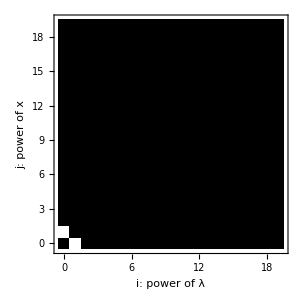

```mathematica
CL1 = CoeffSeriesPerGaus[{0,1,0,0,0,0,0,0,0,0},1];
Plotcoeffs[CL1]
```

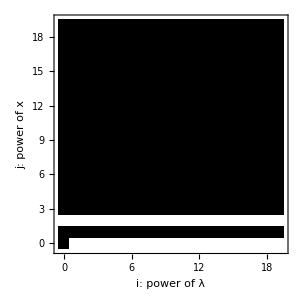

```mathematica
CL2 = CoeffSeriesPerGaus[{0,0,1,0,0,0,0,0,0,0},1];
Plotcoeffs[CL2]
```

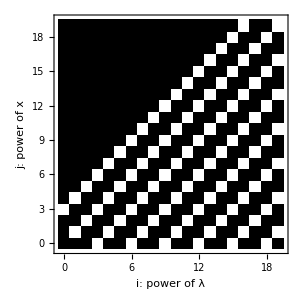

```mathematica
CL3 = CoeffSeriesPerGaus[{0,0,0,1,0,0,0,0,0,0},1];
Plotcoeffs[CL3]
```

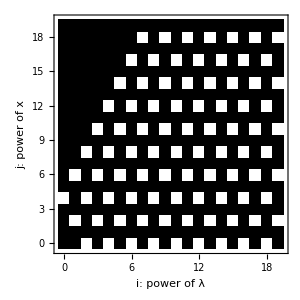

```mathematica
CL4 = CoeffSeriesPerGaus[{0,0,0,0,1,0,0,0,0,0},1];
Plotcoeffs[CL4]
```

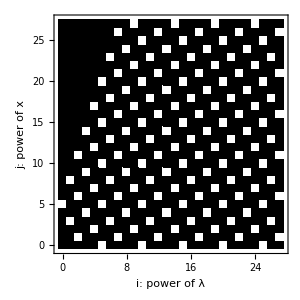

```mathematica
CL5 = CoeffSeriesPerGaus[{0,0,0,0,0,1,0,0,0,0,0,0,0,0},1];
Plotcoeffs[CL5]
```

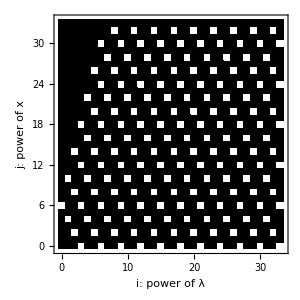

```mathematica
CL6 = CoeffSeriesPerGaus[{0,0,0,0,0,0,1,0,0,0,0,0,0,0, 0, 0, 0},1];
Plotcoeffs[CL6]
```

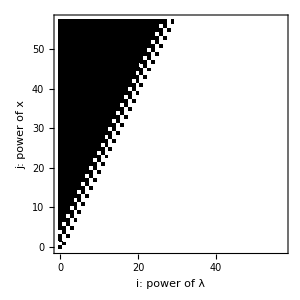

```mathematica
CLbaby = CoeffSeriesPerGaus[{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1];
Plotcoeffs[CLbaby]
```

## Comparing to P-code

```mathematica
ObtGInt[{0,0,b,0,0,0}, a]
```

1/(√a)√(2 π) 𝔼[b/a+b^2/a^2+(4 b^3)/(3 a^3)+(2 b^4)/a^4+(16 b^5)/(5 a^5)+(16 b^6)/(3 a^6)+(64 b^7)/(7 a^7)+(16 b^8)/a^8+(256 b^9)/(9 a^9)+(256 b^10)/(5 a^10)+(1024 b^11)/(11 a^11)]

```mathematica
ObtGInt[{0,0,0,0}, a - 2*b] (*Agrees*)
```

(√(2 π))/(√(a-2 b))

```mathematica
ObtGInt[{0,0,0,b,0,0,0,0}, a] (*Agrees*)
```

(√(2 π) 𝔼[(15 b^2)/(2 a^3)+(405 b^4)/a^6+(89505 b^6)/(2 a^9)+(7413930 b^8)/a^12+(1630244475 b^10)/a^15])/(√a)

```mathematica
ObtGInt[{0,0,0,0,b,0,0,0}, a] (*Agrees except the last coefficient*)
```

1/(√a)√(2 π) 𝔼[(3 b)/a^2+(48 b^2)/a^4+(1584 b^3)/a^6+(78336 b^4)/a^8+(25671168 b^5)/(5 a^10)+(418185216 b^6)/a^12+(247301517312 b^7)/(7 a^14)]

```mathematica
ObtGInt[{0,0,0,0,0,b,0,0}, a](*Agrees except the last coefficient*)
```

(√(2 π) 𝔼[(945 b^2)/(2 a^5)+(27168750 b^4)/a^10+(3181655531250 b^6)/a^15])/(√a)

```mathematica
ObtGInt[{0,0,0,0,0,0,b,0}, a](*Agrees except the last two coefficients*)
```

(√(2 π) 𝔼[(15 b)/a^3+(5085 b^2)/a^6+(5666400 b^3)/a^9+(6374367900 b^4)/a^12+(6940244851200 b^5)/a^15])/(√a)

```mathematica
ObtGInt[{-c,b}, 2a]
```

(√π 𝔼[b^2/(4 a)-c])/(√a)

## Testing out 0-dimensional QFT examples

```mathematica
ObtGIntSimpel[v_, a_]:= Module[{C, dim ,rows,cols, Z}, C= CoeffSeriesPerGaus[v, a]; dim = Dimensions[C]; rows= dim[[1]];cols=dim[[2]];
Z= Sum[1/ ((i-1)! *(j-1)!)* C[[i,j]] * λ^(i-1)*x^(j-1),{i,1,rows}, {j,1,cols}];  Sqrt[2*Pi]*a^(-1/2)*𝔼[FullSimplify[Z/.λ->1/.Thread[x->0]] //TraditionalForm]]
```

```mathematica
ObtGIntSimpel[{0,J,0,0,-ϵ/24,0,0, 0,0}, m^2]
```

1/(√(m^2))𝔼[1/(69672960 m^34)(34836480 J^2 m^32+105 ϵ^8 (428807006 J^2+24886651 m^2)-2903040 m^26 ϵ (J^4+6 J^2 m^2+3 m^4)-240 ϵ^7 (57984696 J^6+76179943 J^4 m^2+36054354 J^2 m^4+2575311 m^6)+483840 m^20 ϵ^2 (2 J^6+21 J^4 m^2+48 J^2 m^4+12 m^6)-241920 m^14 ϵ^3 (2 J^8+32 J^6 m^2+149 J^4 m^4+198 J^2 m^6+33 m^8)+1120 ϵ^6 (72416 J^10+510570 J^8 m^2+1799142 J^6 m^4+2892051 J^4 m^6+1633536 J^2 m^8+136128 m^10)+6720 m^8 ϵ^4 (44 J^10+981 J^8 m^2+7368 J^6 m^4+21276 J^4 m^6+19584 J^2 m^8+2448 m^10)-448 m^2 ϵ^5 (455 J^12+13326 J^10 m^2+143685 J^8 m^4+691740 J^6 m^6+1431450 J^4 m^8+1002780 J^2 m^10+100278 m^12))]

Again off by sqrt{2\pi}
 term equals  1/2m^2 as expected
 term equals -1/8m^4 as expected
 term equals -1/24m^8 not -35/192m^8 which is what it should be 
 term equals 7/48m^12 not 385/1024 m^12 which is what it should be
 term equals 1/72m^14 not 1001/6144 m^14 which is what it should be

```mathematica
ObtZSimpel[v_, a_]:= Module[{C, dim ,rows,cols, Z}, C= CoeffSeriesPerGaus[v, a]; dim = Dimensions[C]; rows= dim[[1]];cols=dim[[2]];
Z= Sum[1/ ((i-1)! *(j-1)!)* C[[i,j]] * λ^(i-1)*x^(j-1),{i,1,rows}, {j,1,cols}];  FullSimplify[Z/.λ->1/.Thread[x->0]]]
```

```mathematica
Collect[ObtZSimpel[{0,J,0,0,-ϵ/24,0,0, 0,0}, m^2], {J, ϵ}]
```

-ϵ/(8 m^4)+ϵ^2/(12 m^8)-(11 ϵ^3)/(96 m^12)+(17 ϵ^4)/(72 m^16)-(91 J^12 ϵ^5)/(31104 m^32)-(619 ϵ^5)/(960 m^20)+(709 ϵ^6)/(324 m^24)-(858437 ϵ^7)/(96768 m^28)+(24886651 ϵ^8)/(663552 m^32)+J^10 ((11 ϵ^4)/(2592 m^26)-(2221 ϵ^5)/(25920 m^30)+(2263 ϵ^6)/(1944 m^34))+J^8 (-ϵ^3/(144 m^20)+(109 ϵ^4)/(1152 m^24)-(3193 ϵ^5)/(3456 m^28)+(9455 ϵ^6)/(1152 m^32))+J^6 (ϵ^2/(72 m^14)-ϵ^3/(9 m^18)+(307 ϵ^4)/(432 m^22)-(427 ϵ^5)/(96 m^26)+(299857 ϵ^6)/(10368 m^30)-(115049 ϵ^7)/(576 m^34))+J^4 (-ϵ/(24 m^8)+(7 ϵ^2)/(48 m^12)-(149 ϵ^3)/(288 m^16)+(197 ϵ^4)/(96 m^20)-(15905 ϵ^5)/(1728 m^24)+(107113 ϵ^6)/(2304 m^28)-(10882849 ϵ^7)/(41472 m^32))+J^2 (1/(2 m^2)-ϵ/(4 m^6)+ϵ^2/(3 m^10)-(11 ϵ^3)/(16 m^14)+(17 ϵ^4)/(9 m^18)-(619 ϵ^5)/(96 m^22)+(709 ϵ^6)/(27 m^26)-(858437 ϵ^7)/(6912 m^30)+(214403503 ϵ^8)/(331776 m^34))

```mathematica
x:= -ϵ/(8 m^4)+ϵ^2/(12 m^8) + (ϵ^2*J^6)/(72 m^14)  -(ϵ*J^4)/(24 m^8) + (7*ϵ^2*J^4)/(48 m^12)+J^2/(2 m^2)-(ϵ *J^2)/(4 m^6) + (ϵ^2 *J^2)/(3 m^10);
```

```mathematica
y:= 1 + x +x^2/2 + x^3/6 + x^4/24 + x^5/120;
```

```mathematica
Collect[Coefficient[y,ϵ^2*J^4] , m]
```

385/(1024 m^12)

```mathematica
Collect[Coefficient[y,ϵ^2*J^6] ,m]
```

1001/(6144 m^14)

Fubini - Comparing with Picard iterations

```mathematica
ObtGIntSimpel[{-c*y^2/2 + ξ2*y,-b*y +  ξ1,0,0}, a]
```

(√(2 π) 𝔼[(ξ1-b y)^2/(2 a)-(c y^2)/2+ξ2 y])/(√a)

```mathematica
ObtGIntSimpel[{ξ1^2/(2*a), 0-ξ1*b/a + ξ2,0,0,0},c-b^2/a]
```

(√(2 π) 𝔼[(ξ2 (a ξ2-2 b ξ1)+c ξ1^2)/(2 a c-2 b^2)])/(√(-b^2/a+c))

```mathematica
ObtGIntSimpel[{-c*y^2/2 + ξ2*y^2,-b*y ,0,0}, a-2*ξ1]
```

(√(2 π) 𝔼[1/2 y^2 (b^2/(a-2 ξ1)-c+2 ξ2)])/(√(a-2 ξ1))

```mathematica
ObtGIntSimpel[{0,0 ,0,0}, c-2*ξ2 -b^2 / (a - 2*ξ1)]
```

(√(2 π) 𝔼[0])/(√(c-b^2/(a-2 ξ1)-2 ξ2))

```mathematica
ObtGIntSimpel[{-c*y^2/2 ,(ξ-b)*y ,0,0}, a]
```

(√(2 π) 𝔼[(y^2 ((b-ξ)^2-a c))/(2 a)])/(√a)

```mathematica
ObtGIntSimpel[{0,0,0,0}, -((b-ξ)^2-ac)/(a)]
```

(√(2 π) 𝔼[0])/(√((ac-(b-ξ)^2)/a))

```mathematica
ObtGIntSimpel[{-c*y^2/2 + ξ4*y^2+ ξ2*y,ξ1-b*y ,0,0}, a-2*ξ3]
```

(√(2 π) 𝔼[(ξ1-b y)^2/(2 (a-2 ξ3))-(c y^2)/2+ξ4 y^2+ξ2 y])/(√(a-2 ξ3))

```mathematica
ObtGIntSimpel[{ ξ1^2/( 2*(a - 2*ξ3)), ξ2- b*ξ1/ (a - 2*ξ3),0,0}, c-2*ξ4 -b^2 / (a - 2*ξ3)]
```

(√(2 π) 𝔼[(ξ2^2 (a-2 ξ3)-2 b ξ1 ξ2+c ξ1^2-2 ξ1^2 ξ4)/(2 (a-2 ξ3) (c-2 ξ4)-2 b^2)])/(√(c-b^2/(a-2 ξ3)-2 ξ4))